```mathematica
(* HW_1 *)
```

```mathematica
Subscript[ϕ, ξ][t_]=(1-p+p*Exp[ⅈ*t])^n
```

(1-p+ⅇ^(ⅈ t) p)^n

Derivative::novar: ∂ϕ cannot be interpreted. A partial derivative requires a subscript differentiation variable.

```mathematica
E1=D[Subscript[ϕ, ξ][t], t]/ⅈ
```

ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n)

```mathematica
ⅇ^(i t) i n p (1-p+ⅇ^(i t) p)^(-1+n)/.t ->0
```

i n p

```mathematica
E2=D[D[Subscript[ϕ, ξ][t], t], t]/ⅈ^2
```

ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)+ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n)

```mathematica
ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)+ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n)/. t->0
```

n p+(-1+n) n p^2

```mathematica
n p+(-1+n) n p^2//Expand
```

n p-n p^2+n^2 p^2

```mathematica
DE=E2-E1^2
```

```mathematica
ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)+ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n)-ⅇ^(2 ⅈ t) n^2 p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+2 n)/.t->0
```

```mathematica
n p+(-1+n) n p^2-n^2 p^2//Simplify
```

-n (-1+p) p

```mathematica
ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)+ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n)-ⅇ^(2 ⅈ t) n^2 p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+2 n)/.t->0
```

```mathematica
n p+(-1+n) n p^2-n^2 p^2//Simplify
```

-n (-1+p) p

```mathematica
E3=D[D[D[Subscript[ϕ, ξ][t], t], t], t]/ⅈ^3
```

ⅈ (-ⅈ ⅇ^(3 ⅈ t) (-2+n) (-1+n) n p^3 (1-p+ⅇ^(ⅈ t) p)^(-3+n)-3 ⅈ ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)-ⅈ ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n))

```mathematica
ⅈ (-ⅈ ⅇ^(3 ⅈ t) (-2+n) (-1+n) n p^3 (1-p+ⅇ^(ⅈ t) p)^(-3+n)-3 ⅈ ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)-ⅈ ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n))/.t->0
```

```mathematica
ⅈ (-ⅈ n p-3 ⅈ (-1+n) n p^2-ⅈ (-2+n) (-1+n) n p^3)//Simplify
```

```mathematica
n p (1+3 (-1+n) p+(2-3 n+n^2) p^2)//Expand
```

n p-3 n p^2+3 n^2 p^2+2 n p^3-3 n^2 p^3+n^3 p^3

```mathematica
ⅈ (-ⅈ n p-3 ⅈ (-1+n) n p^2-ⅈ (-2+n) (-1+n) n p^3)//Simplify
```

n p (1+3 (-1+n) p+(2-3 n+n^2) p^2)

```mathematica
ⅈ (-ⅈ ⅇ^(3 ⅈ t) (-2+n) (-1+n) n p^3 (1-p+ⅇ^(ⅈ t) p)^(-3+n)-3 ⅈ ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)-ⅈ ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n))/.t->0
```

```mathematica
ⅈ (-ⅈ n p-3 ⅈ (-1+n) n p^2-ⅈ (-2+n) (-1+n) n p^3)//Simplify
```

```mathematica
n p (1+3 (-1+n) p+(2-3 n+n^2) p^2)//Expand
```

```mathematica
n p-3 n p^2+3 n^2 p^2+2 n p^3-3 n^2 p^3+n^3 p^3
```

n p-3 n p^2+3 n^2 p^2+2 n p^3-3 n^2 p^3+n^3 p^3

```mathematica
M3=E3-3*E2*E1+2*E1^3/.t->0//Simplify//Expand
```

n p-3 n p^2+2 n p^3

```mathematica
D[D[Subscript[ϕ, ξ][t], t], t]/ⅈ^3
```

```mathematica
ⅈ (-ⅇ^(2 ⅈ t) (-1+n) n p^2 (1-p+ⅇ^(ⅈ t) p)^(-2+n)-ⅇ^(ⅈ t) n p (1-p+ⅇ^(ⅈ t) p)^(-1+n))//Simplify
```

```mathematica
-ⅈ ⅇ^(ⅈ t) n p (1+(-1+ⅇ^(ⅈ t)) p)^(-2+n) (1+(-1+ⅇ^(ⅈ t) n) p)//Expand
```

-ⅈ ⅇ^(ⅈ t) n p (1+(-1+ⅇ^(ⅈ t)) p)^(-2+n)+ⅈ ⅇ^(ⅈ t) n p^2 (1+(-1+ⅇ^(ⅈ t)) p)^(-2+n)-ⅈ ⅇ^(2 ⅈ t) n^2 p^2 (1+(-1+ⅇ^(ⅈ t)) p)^(-2+n)

```mathematica
w[s_]:=(1/(2 π σ^2))^(1/2)*Exp[-(s-L)^2/(2 σ^2)]
```

```mathematica
S_mean=∫_(-∞)^(+∞) s w[s]ⅆs
```

ConditionalExpression[L,Re[σ^2]≥0]

```mathematica
l
```

l

```mathematica
∫_0 Exp[ξ (ⅈ t -1)]ⅆξ

y[t_]:=1/(1-ⅈt)
```

ConditionalExpression[ⅈ/(ⅈ+t),Im[t]>-1]

Integrate::idiv: Integral of ⅇ^(ⅈ (ⅈ+t) ξ) does not converge on {-∞,∞}.

Integrate::nodiffd: ∫_(-∞)^(+∞)  cannot be interpreted. Integrals are entered in the form ∫f ⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Integrate/nodiffd",
ButtonNote->"Integrate::nodiffd"]

```mathematica
∫_0^(+∞) Exp[ξ (ⅈ t -1)]ⅆξ

F_y[t]
```

ConditionalExpression[ⅈ/(ⅈ+t),Im[t]>-1]

F_y[t]

```mathematica
1/(2 π)∫_(-∞)^(+∞) Exp[- x ⅈ t] y[t]^2ⅆt
```

Integrate::idiv: Integral of ⅇ^(-ⅈ t x)/(-1+ⅈt)^2 does not converge on {-∞,∞}.

(∫_(-∞)^∞ ⅇ^(-ⅈ t x)/(1-ⅈt)^2 ⅆt)/(2 π)

```mathematica
y[t]
```

1/(1-ⅈt)

```mathematica
∫_0^ϕ t Exp[-t]ⅆt
```

1-ⅇ^-ϕ (1+ϕ)

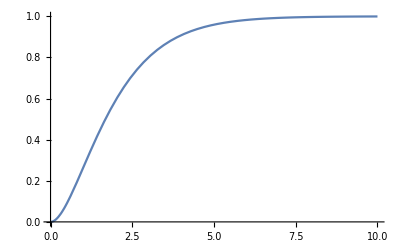

```mathematica
Plot[Out[41], {ϕ, 0, 10}]
```